PREMIER LEAGUE STATISTIKA

TABELA PREMIER LEAGUE

```mathematica
SetDirectory["C:\\Users\\Igre\\Documents\\ROM\\Projekt_1"]
```

C:\Users\Igre\Documents\ROM\Projekt_1

```mathematica
Directory[]
```

C:\Users\Igre\Documents\ROM\Projekt_1

```mathematica
TabelaPodatkov = Import["Lestvica.xlsx"]//First;
TabelaPodatkov//TableForm
```

Mesto | Klub | Tekme | Zmage | Remiji | Porazi | Dani zadetki | Prejeti zadetki | Gol razlika | Točke | Rumeni | Rdeči | Domače tekme | Gledalci | Štadion | Vrednost kluba
1. | Liverpool | 20. | 17. | 3. | 0. | 48. | 8. | 40. | 54. | 18. | 1. | 10. | 527420. | 54074. | 9.51×10^8
2. | Manchester City | 20. | 15. | 2. | 3. | 54. | 16. | 38. | 47. | 21. | 1. | 10. | 540674. | 55097. | 1.13×10^9
3. | Tottenham Hotspur | 20. | 15. | 0. | 5. | 43. | 21. | 22. | 45. | 28. | 1. | 9. | 460239. | 90000. | 8.265×10^8
4. | Chelsea | 20. | 13. | 4. | 3. | 38. | 16. | 22. | 43. | 27. | 0. | 10. | 404946. | 41837. | 9.0725×10^8
5. | Arsenal | 20. | 11. | 5. | 4. | 42. | 30. | 12. | 38. | 38. | 0. | 10. | 599015. | 60362. | 6.045×10^8
6. | Manchester United | 20. | 10. | 5. | 5. | 41. | 32. | 9. | 35. | 39. | 3. | 10. | 744997. | 75731. | 7.74×10^8
7. | Wolverhampton Wanderers | 20. | 8. | 5. | 7. | 23. | 23. | 0. | 29. | 35. | 0. | 10. | 310220. | 31700. | 2.315×10^8
8. | Leicester City | 20. | 8. | 4. | 8. | 24. | 23. | 1. | 28. | 31. | 4. | 10. | 319354. | 32500. | 3.465×10^8
9. | Watford | 20. | 8. | 4. | 8. | 27. | 28. | -1. | 28. | 33. | 2. | 11. | 223051. | 22100. | 1.85×10^8
10. | Everton | 20. | 7. | 6. | 7. | 31. | 30. | 1. | 27. | 28. | 2. | 10. | 384159. | 40157. | 4.455×10^8
11. | West Ham United | 20. | 8. | 3. | 9. | 27. | 30. | -3. | 27. | 41. | 1. | 10. | 568956. | 60000. | 2.98×10^8
12. | Bournemouth | 20. | 8. | 2. | 10. | 28. | 37. | -9. | 26. | 32. | 1. | 10. | 105542. | 11464. | 2.105×10^8
13. | Brighton and Hove Albion | 20. | 7. | 4. | 9. | 22. | 27. | -5. | 25. | 36. | 3. | 10. | 304913. | 30750. | 1.765×10^8
14. | Crystal Palace | 20. | 5. | 4. | 11. | 17. | 26. | -9. | 19. | 34. | 1. | 10. | 254865. | 26255. | 2.2225×10^8
15. | Newcastle United | 20. | 4. | 6. | 10. | 15. | 27. | -12. | 18. | 29. | 2. | 10. | 509293. | 52409. | 1.76×10^8
16. | Cardiff City | 20. | 5. | 3. | 12. | 19. | 38. | -19. | 18. | 32. | 1. | 10. | 309084. | 33000. | 9.425×10^7
17. | Southampton | 20. | 3. | 6. | 11. | 21. | 38. | -17. | 15. | 43. | 2. | 10. | 298205. | 32689. | 2.611×10^8
18. | Burnley | 20. | 4. | 3. | 13. | 19. | 41. | -22. | 15. | 40. | 0. | 10. | 204229. | 22546. | 1.7825×10^8
19. | Fulham | 20. | 3. | 5. | 12. | 18. | 43. | -25. | 14. | 34. | 2. | 10. | 242519. | 25700. | 2.475×10^8
20. | Huddersfield Town | 20. | 2. | 4. | 14. | 12. | 35. | -23. | 10. | 28. | 2. | 10. | 227702. | 24500. | 1.271×10^8

```mathematica
TabelaTock = Import["Tocke.xlsx"]//First;
TabelaTock // TableForm;
```

OSNOVNE FUNKCIJE

```mathematica
Ogrodje[podatki_]:=First[podatki]
Ogrodje[TabelaPodatkov];
```

```mathematica
Podatki[podatki_]:=Rest[podatki]
```

```mathematica
Podatki[TabelaPodatkov];
```

```mathematica
IndeksStolpca[podatki_,stolpec_]:=Position[Ogrodje[podatki],stolpec]//First//First
IndeksStolpca[TabelaPodatkov,"Točke"];
```

```mathematica
Vrstica[podatki_,i_]:=Podatki[podatki][[i]]
Vrstica[TabelaPodatkov, 20];
```

```mathematica
Stolpec[podatki_,stolpec_]:=Transpose[Podatki[podatki]][[IndeksStolpca[podatki,stolpec]]]
```

```mathematica
Stolpec[TabelaPodatkov,"Dani zadetki"];
```

```mathematica
OgrodjeTock[podatki_] := First[podatki]
PodatkiTock[podatki_] := Rest[podatki]
IndeksStolpcaTock[podatki_,stolpec_]:=Position[OgrodjeTock[podatki],stolpec]//First //First
StolpecTock[podatki_,stolpec_]:=Transpose[PodatkiTock[podatki]][[IndeksStolpcaTock[podatki,stolpec]]]
```

STATISTIKA

Povprečje golov na tekmo:

```mathematica
Tekme[podatki_]:=Mean[Stolpec[podatki,"Tekme"]]
PovprecjeDZ[podatki_] := Mean[Stolpec[podatki,"Dani zadetki"]]
```

```mathematica
PovprecjeDZ[TabelaPodatkov]
```

28.45

```mathematica
PovprecjeGolovNaTekmo= PovprecjeDZ[TabelaPodatkov] /Tekme[TabelaPodatkov]* 2
```

2.845

Povprečje rumenih kartonov na tekmo:

```mathematica
PovprecjeRumenih[podatki_] :=Mean[Stolpec[podatki,"Rumeni"]]
PovprecjeRumenih[TabelaPodatkov]
```

32.35

```mathematica
PovpreceRumenihNaTekmo = PovprecjeRumenih[TabelaPodatkov]/Tekme[TabelaPodatkov]*2
```

3.235

Povprečje rdečih kartonov na tekmo:

```mathematica
PovprecjeRdecih[podatki_] :=Mean[Stolpec[podatki,"Rdeči"]]
PovprecjeRdecih[TabelaPodatkov]
```

1.45

```mathematica
PovprecjeRdecihNaTekmo = PovprecjeRdecih[TabelaPodatkov]/Tekme[TabelaPodatkov]*2
```

0.145

Povprečna vrednost kluba:

```mathematica
PovprecnaVrednostKluba[podatki_]:=Mean[Stolpec[podatki,"Vrednost kluba"]]
PovprecnaVrednostKluba[TabelaPodatkov]
```

4.1966×10^8

Povprečje gledalcev na tekmo:

```mathematica
PovprecjeGledalcev[podatki_]:=Mean[Stolpec[podatki, "Gledalci"]]
PovprecjeGledalcev[TabelaPodatkov]
```

376969.

```mathematica
PovrecjeGledalcevNaTekmo= PovprecjeGledalcev[TabelaPodatkov]/Tekme[TabelaPodatkov]*2
```

37696.9

Skupno število gledalcev:

```mathematica
Gledalci[podatki_]:=Total[Stolpec[podatki,"Gledalci"]]
Gledalci[TabelaPodatkov]
```

7.53938×10^6

Povprečna zasedenost v odstotkih:

```mathematica
ZasedenostPoKlubih =((Stolpec[TabelaPodatkov,"Gledalci"]/Stolpec[TabelaPodatkov,"Domače tekme"])/Stolpec[TabelaPodatkov,"Štadion"])*100
```

{97.5367,98.1313,56.8196,96.7914,99.2371,98.3741,97.8612,98.2628,91.7528,95.6643,94.826,92.0639,99.1587,97.0729,97.1766,93.6618,91.2249,90.5833,94.3654,92.9396}

```mathematica
Zasedenost= Mean[ZasedenostPoKlubih]
```

93.6752

Dodajanje zasedenosti tekem v tabelo:

```mathematica
DodajStolpec[podatki_,imeStolpca_,stolpec_]:= Append[Transpose[podatki], Prepend[stolpec, imeStolpca]] // Transpose
NadgrajenaTabela=DodajStolpec[TabelaPodatkov,"Povprečna zasedenost %",ZasedenostPoKlubih]//TableForm
```

Mesto | Klub | Tekme | Zmage | Remiji | Porazi | Dani zadetki | Prejeti zadetki | Gol razlika | Točke | Rumeni | Rdeči | Domače tekme | Gledalci | Štadion | Vrednost kluba | Povprečna zasedenost %
1. | Liverpool | 20. | 17. | 3. | 0. | 48. | 8. | 40. | 54. | 18. | 1. | 10. | 527420. | 54074. | 9.51×10^8 | 97.5367
2. | Manchester City | 20. | 15. | 2. | 3. | 54. | 16. | 38. | 47. | 21. | 1. | 10. | 540674. | 55097. | 1.13×10^9 | 98.1313
3. | Tottenham Hotspur | 20. | 15. | 0. | 5. | 43. | 21. | 22. | 45. | 28. | 1. | 9. | 460239. | 90000. | 8.265×10^8 | 56.8196
4. | Chelsea | 20. | 13. | 4. | 3. | 38. | 16. | 22. | 43. | 27. | 0. | 10. | 404946. | 41837. | 9.0725×10^8 | 96.7914
5. | Arsenal | 20. | 11. | 5. | 4. | 42. | 30. | 12. | 38. | 38. | 0. | 10. | 599015. | 60362. | 6.045×10^8 | 99.2371
6. | Manchester United | 20. | 10. | 5. | 5. | 41. | 32. | 9. | 35. | 39. | 3. | 10. | 744997. | 75731. | 7.74×10^8 | 98.3741
7. | Wolverhampton Wanderers | 20. | 8. | 5. | 7. | 23. | 23. | 0. | 29. | 35. | 0. | 10. | 310220. | 31700. | 2.315×10^8 | 97.8612
8. | Leicester City | 20. | 8. | 4. | 8. | 24. | 23. | 1. | 28. | 31. | 4. | 10. | 319354. | 32500. | 3.465×10^8 | 98.2628
9. | Watford | 20. | 8. | 4. | 8. | 27. | 28. | -1. | 28. | 33. | 2. | 11. | 223051. | 22100. | 1.85×10^8 | 91.7528
10. | Everton | 20. | 7. | 6. | 7. | 31. | 30. | 1. | 27. | 28. | 2. | 10. | 384159. | 40157. | 4.455×10^8 | 95.6643
11. | West Ham United | 20. | 8. | 3. | 9. | 27. | 30. | -3. | 27. | 41. | 1. | 10. | 568956. | 60000. | 2.98×10^8 | 94.826
12. | Bournemouth | 20. | 8. | 2. | 10. | 28. | 37. | -9. | 26. | 32. | 1. | 10. | 105542. | 11464. | 2.105×10^8 | 92.0639
13. | Brighton and Hove Albion | 20. | 7. | 4. | 9. | 22. | 27. | -5. | 25. | 36. | 3. | 10. | 304913. | 30750. | 1.765×10^8 | 99.1587
14. | Crystal Palace | 20. | 5. | 4. | 11. | 17. | 26. | -9. | 19. | 34. | 1. | 10. | 254865. | 26255. | 2.2225×10^8 | 97.0729
15. | Newcastle United | 20. | 4. | 6. | 10. | 15. | 27. | -12. | 18. | 29. | 2. | 10. | 509293. | 52409. | 1.76×10^8 | 97.1766
16. | Cardiff City | 20. | 5. | 3. | 12. | 19. | 38. | -19. | 18. | 32. | 1. | 10. | 309084. | 33000. | 9.425×10^7 | 93.6618
17. | Southampton | 20. | 3. | 6. | 11. | 21. | 38. | -17. | 15. | 43. | 2. | 10. | 298205. | 32689. | 2.611×10^8 | 91.2249
18. | Burnley | 20. | 4. | 3. | 13. | 19. | 41. | -22. | 15. | 40. | 0. | 10. | 204229. | 22546. | 1.7825×10^8 | 90.5833
19. | Fulham | 20. | 3. | 5. | 12. | 18. | 43. | -25. | 14. | 34. | 2. | 10. | 242519. | 25700. | 2.475×10^8 | 94.3654
20. | Huddersfield Town | 20. | 2. | 4. | 14. | 12. | 35. | -23. | 10. | 28. | 2. | 10. | 227702. | 24500. | 1.271×10^8 | 92.9396

GRAFI

```mathematica
klubi = {"LIV","MCI", "TOT", "CHE", "ARS", "MUN", "WOL", "LEI", "WAT", "EVE", "WHU", "BOU", "BHA", "CRY", "NEW", "CAR", "SOU", "BUR", "FUL", "HUD"}
```

{LIV,MCI,TOT,CHE,ARS,MUN,WOL,LEI,WAT,EVE,WHU,BOU,BHA,CRY,NEW,CAR,SOU,BUR,FUL,HUD}

```mathematica
ListPlot[{StolpecTock[TabelaTock,"Liverpool"],StolpecTock[TabelaTock,"Manchester City"],StolpecTock[TabelaTock,"Tottenham Hotspur"],StolpecTock[TabelaTock,"Chelsea"],StolpecTock[TabelaTock,"Arsenal"],StolpecTock[TabelaTock,"Manchester United"],StolpecTock[TabelaTock,"Wolverhampton Wanderers"],StolpecTock[TabelaTock,"Leicester City"],StolpecTock[TabelaTock,"Watford"],StolpecTock[TabelaTock,"Everton"],StolpecTock[TabelaTock,"West Ham United"],StolpecTock[TabelaTock,"Bournemouth"],StolpecTock[TabelaTock,"Brighton and Hove Albion"],StolpecTock[TabelaTock,"Crystal Palace"],StolpecTock[TabelaTock,"Newcastle United"],StolpecTock[TabelaTock,"Cardiff City"],StolpecTock[TabelaTock,"Southampton"],StolpecTock[TabelaTock,"Burnley"],StolpecTock[TabelaTock,"Fulham"],StolpecTock[TabelaTock,"Huddersfield Town"]},Joined->True, PlotLabels->{"Liverpool", "Manchester City","Tottenham Hotspur","Chelsea","Arsenal","Manchester United","Wolverhampton Wanderers","Leicester City","Watford","Everton","West Ham United","Bournemouth","Brighton and Hove Albion","Crystal Palace","Newcastle United","Cardiff City","Southampton","Burnley","Fulham","Huddersfield Town"},PlotTheme->"Business",FrameLabel->{"Krogi", "Točke"}, PlotLabel->Style["Točke klubov čez sezono",FontSize->24, FontColor->Purple]]
```

-Graphics-

```mathematica
PieChart3D[Stolpec[TabelaPodatkov,"Vrednost kluba"],PlotTheme->"Web", ChartLabels-> klubi,PlotLabel->Style["Vrednost klubov",FontSize->24,FontColor->Purple]]
```

-Graphics3D-

Prvih pet klubov predstavlja kar polovico vrednosti Premier League.

```mathematica
VrednostVsakeTocke = Stolpec[TabelaPodatkov,"Vrednost kluba"]/Stolpec[TabelaPodatkov,"Točke"];
```

```mathematica
BarChart[VrednostVsakeTocke ,PlotTheme->"Detailed",ChartStyle-> "Rainbow",ChartLabels-> klubi, FrameLabel-> {"Klubi"},PlotLabel->Style["Vrednost vsake točke glede na vrednost kluba",FontSize->20,FontColor->Purple]]
```

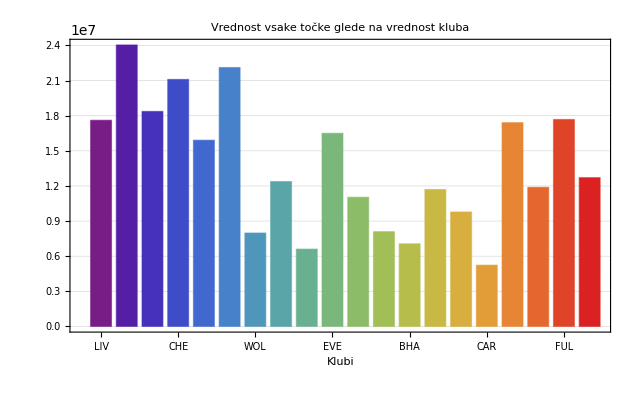

Zanimivo je videti, da so igralci najboljših klubov ovrednoteni tako visoko, da ne glede koliko točk osvajajo, izgledajo precenjeni.

```mathematica
Kaznovanost = Stolpec[TabelaPodatkov,"Rumeni"] + (3*(Stolpec[TabelaPodatkov,"Rdeči"]))
```

{21.,24.,31.,27.,38.,48.,35.,43.,39.,34.,44.,35.,45.,37.,35.,35.,49.,40.,40.,34.}

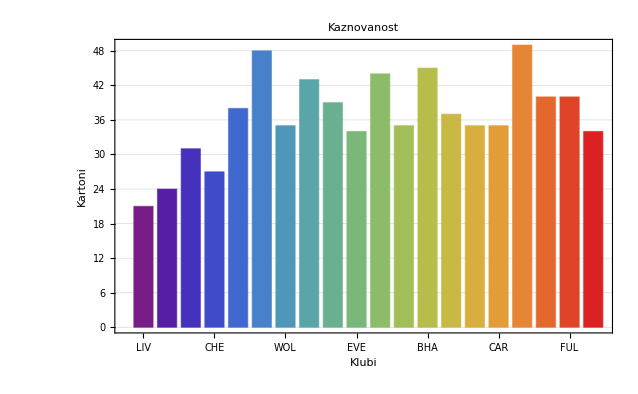

```mathematica
BarChart[Kaznovanost,PlotTheme->"Detailed",ChartStyle-> "Rainbow",ChartLabels-> klubi, FrameLabel-> {"Klubi","Kartoni"},PlotLabel->Style["Kaznovanost",FontSize->24,FontColor->Purple]]
```

Pričakoval sem, da bodo imeli nižje uvrščeni klubi več kartonov, vendar izstopajo samo prvi štirje klubi. En rdeči karton sem ovrednotil s tremi rumenimi kartoni.

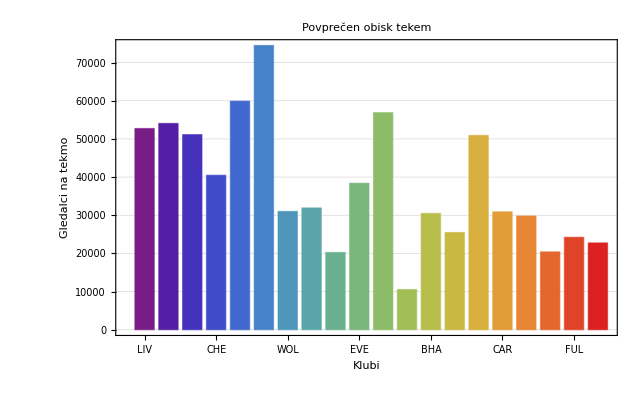

```mathematica
BarChart[{Stolpec[TabelaPodatkov,"Gledalci"]/Stolpec[TabelaPodatkov,"Domače tekme"]}, ChartLabels->klubi,FrameLabel->{"Klubi","Gledalci na tekmo"},PlotTheme -> "Detailed",ChartStyle->"Rainbow",PlotLabel->Style["Povprečen obisk tekem",FontSize->24,FontColor->Purple]]
```

```mathematica
Zdruzitev = Transpose[{Stolpec[TabelaPodatkov,"Dani zadetki"],Stolpec[TabelaPodatkov,"Prejeti zadetki"],Stolpec[TabelaPodatkov,"Točke"]}]
```

{{48.,8.,54.},{54.,16.,47.},{43.,21.,45.},{38.,16.,43.},{42.,30.,38.},{41.,32.,35.},{23.,23.,29.},{24.,23.,28.},{27.,28.,28.},{31.,30.,27.},{27.,30.,27.},{28.,37.,26.},{22.,27.,25.},{17.,26.,19.},{15.,27.,18.},{19.,38.,18.},{21.,38.,15.},{19.,41.,15.},{18.,43.,14.},{12.,35.,10.}}

```mathematica
RectangleChart3D[Zdruzitev, ChartStyle-> "Rainbow",PlotTheme->"Detailed",ChartLabels-> klubi]
```

Višina stolpcev predstavlja osvojene točke, širina dane zadetke in globina prejete zadetke.

Najbolj izstopata Arsenal in Manchester United, ki sta kljub veliko zadetkom osvojila dokaj malo točk, kar gre verjetno pripisati slabši obrambi.

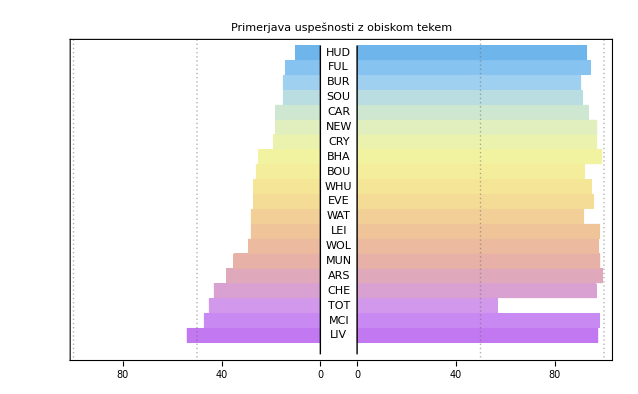

```mathematica
PairedBarChart[{Stolpec[TabelaPodatkov,"Točke"]},{((Stolpec[TabelaPodatkov,"Gledalci"]/Stolpec[TabelaPodatkov,"Domače tekme"])/Stolpec[TabelaPodatkov,"Štadion"])*100},ChartLabels->klubi,ChartStyle->"Pastel",PlotTheme->"Detailed",PlotLabel->Style["Primerjava uspešnosti z obiskom tekem", FontSize->20,FontColor->Purple]]
```

Leva stran predstavlja osvojene točke, desna pa odstotek zasedenosti štadionov. Tekme so pri vseh klubih dobro zasedene, ne glede na uspeh. Edini ki izstopa je Tottenham, ki pa začasno igra to sezona na drugem štadionu.

VIRI

```mathematica
Hyperlink["https://www.premierleague.com/"]
```

https://www.premierleague.com/

```mathematica
Hyperlink["https://www.worldfootball.net/attendance/eng-premier-league-2018-2019/1/"]
```

https://www.worldfootball.net/attendance/eng-premier-league-2018-2019/1/

```mathematica
Hyperlink["https://www.worldfootball.net/venues/eng-premier-league-2018-2019/"]
```

https://www.worldfootball.net/venues/eng-premier-league-2018-2019/